### Two Trader Equilibrium in the OW Model - Exact Solution

#### Calculate the Nash Equilibrium

Equilibrium Solutions: {{a0→0.720518,a1→-1.43879,b0→0.339349,b1→0.367022}}

Checking the gradient at the Equilibrium.

dCa/da0: 0.

dCa/da1: 0.

dCb/db0: 2.22045×10^-15

dCb/db1: -4.44089×10^-15

Checking the Hessian at the Equilibrium.

Hessian of Ca with respect to {a0, a1}: {{0.703003,-0.161662},{-0.161662,0.703003}}

Hessian of Cb with respect to {b0, b1}: {{70.3003,-16.1662},{-16.1662,70.3003}}

Is Hessian of Ca positive definite? True

Is Hessian of Cb positive definite? True

-Graphics-

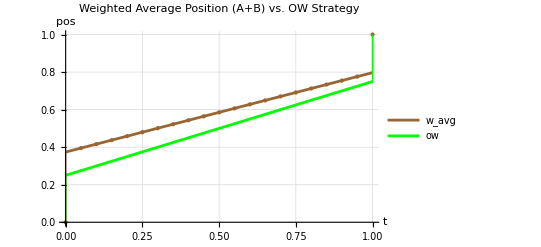

```mathematica
(*Model Parameters*)
rho=2;
lambda=10;

(*Define Cost Functions*)
Ca[a0_,a1_,b0_,b1_]:=Module[{mua,mub,c0,c1,mu,Disp,IDisp},
mua=1-a0-a1;
mub=1-b0-b1;
c0=a0+lambda*b0;
c1=a1+lambda*b1;
mu=mua+lambda*mub;
Disp[t_]:=c0 Exp[-rho t]+mu (1-Exp[-rho t])/rho;
IDisp=Integrate[Disp[t],{t,0,1}];
1/2*(c0*a0+c1*a1)+mua*IDisp+Disp[1]*a1];

Cb[a0_,a1_,b0_,b1_]:=Module[{mua,mub,c0,c1,mu,Disp,IDisp},
mua=1-a0-a1;
mub=1-b0-b1;
c0=a0+lambda*b0;
c1=a1+lambda*b1;
mu=mua+lambda*mub;
Disp[t_]:=c0 Exp[-rho t]+mu (1-Exp[-rho t])/rho;
IDisp=Integrate[Disp[t],{t,0,1}];
lambda*(1/2*(c0*b0+c1*b1)+mub*IDisp+Disp[1]*b1)];

(*Solve for the variables that set all partial derivatives to zero*)
sol=Solve[
{D[Ca[a0,a1,b0,b1],a0]==0,
D[Ca[a0,a1,b0,b1],a1]==0,
D[Cb[a0,a1,b0,b1],b0]==0,
D[Cb[a0,a1,b0,b1],b1]==0},
{a0,a1,b0,b1}
];

(*Display solutions*)
Print["\nEquilibrium Solutions: ",N[sol]];

(*Check if the solution exists before using it*)If[Length[sol]>0,(*Extract solutions*){a0sol,a1sol,b0sol,b1sol}={a0,a1,b0,b1}/. sol[[1]],Print["No solutions found."]];

(*Calculate partial derivatives at the solution point*)evalDCaDa0=D[Ca[a0,a1,b0,b1],a0]/. {a0->a0sol,a1->a1sol,b0->b0sol,b1->b1sol};
evalDCaDa1=D[Ca[a0,a1,b0,b1],a1]/. {a0->a0sol,a1->a1sol,b0->b0sol,b1->b1sol};
evalDCbDb0=D[Cb[a0,a1,b0,b1],b0]/. {a0->a0sol,a1->a1sol,b0->b0sol,b1->b1sol};
evalDCbDb1=D[Cb[a0,a1,b0,b1],b1]/. {a0->a0sol,a1->a1sol,b0->b0sol,b1->b1sol};

(*Print partial derivatives at the solution point*)
Print["\nChecking the gradient at the Equilibrium."]
Print["dCa/da0: ",N[evalDCaDa0]];
Print["dCa/da1: ",N[evalDCaDa1]];
Print["dCb/db0: ",N[evalDCbDb0]];
Print["dCb/db1: ",N[evalDCbDb1]];

(*Calculate Hessians*)
hessianCa=D[Ca[a0,a1,b0,b1],{{a0,a1},2}]/. {a0->a0sol,a1->a1sol,b0->b0sol,b1->b1sol};
hessianCb=D[Cb[a0,a1,b0,b1],{{b0,b1},2}]/. {a0->a0sol,a1->a1sol,b0->b0sol,b1->b1sol};

(*Check if Hessians are positive definite*)isPositiveDefinite[matrix_]:=PositiveDefiniteMatrixQ[matrix];

(*Print Hessians and check positive definiteness*)
Print["\nChecking the Hessian at the Equilibrium."]
Print["Hessian of Ca with respect to {a0, a1}: ",N[hessianCa]];
Print["Hessian of Cb with respect to {b0, b1}: ",N[hessianCb]];
Print["Is Hessian of Ca positive definite? ",isPositiveDefinite[hessianCa]];
Print["Is Hessian of Cb positive definite? ",isPositiveDefinite[hessianCb]];

(*Calculate c0 and mu based on the solutions*)mua=1-a0sol-a1sol;
mub=1-b0sol-b1sol;
c0=a0sol+lambda*b0sol;
mu=mua+lambda* mub;

(*Caclulate values of a(t), b(t), OW(t) over time for plotting*)aFunc[t_]:=Piecewise[{{0,t==0},{a0sol+(1-a0sol-a1sol)*t,0<t<1},{1,t==1}}];
bFunc[t_]:=Piecewise[{{0,t==0},{b0sol+(1-b0sol-b1sol)*t,0<t<1},{1,t==1}}];
ow[t_]:=Piecewise[{{0,t==0},{1/(2+rho)+rho/(2+rho)*t,0<t<1},{1,t==1}}];
wboth[t_] := (aFunc[t] + lambda * bFunc[t]) / (1+lambda)
DispFunc[t_]:=c0 Exp[-rho t]+mu (1-Exp[-rho t])/rho;

(*Plot the trading strategies for A and B*)
eps=0.001;
plot1=Plot[{aFunc[t],bFunc[t],ow[t], t},{t,0,1},PlotStyle->{{Red},{Blue},{Green, Dashed},{Gray,Dotted}},
Epilog->{
Red,PointSize[Medium],Table[Point[{t,aFunc[t]}],{t,0,1,0.05}],Line[{{0,0},{0,aFunc[eps]}}],Line[{{1,aFunc[1-eps]},{1,1}}],
Blue,Line[{{0,0},{0,bFunc[eps]}}],Line[{{1,bFunc[1-eps]},{1,1}}]},PlotLegends->{"a[t]","b[t]","OW[t]","f[t]=t"},PlotLabel->Row[{"Nash Equilibrium Trading Functions\n","ρ = ",rho,", λ = ",lambda}],AxesLabel->{"t","f[t]"},Ticks->Automatic, PlotRange->{0,Automatic}];

(* Plot the price displacement *)
plot2=Plot[DispFunc[t],{t,0,1},PlotStyle->{Green,Dashed},PlotLegends->{"Disp[t]"},PlotLabel->Row[{"Price Displacement D(t)\n","ρ = ",rho,", λ = ",lambda}],AxesLabel->{"t","Disp[t]"},Ticks->Automatic,PlotRange->{0,Automatic},GridLines->Automatic];

(*Display the plots*)
GraphicsGrid[{{plot1},{plot2}},Spacings->{2,2}]

(*Weighted Average Trading Schedule vs. OW*)
plot3 = Plot[{wboth[t],ow[t]}, {t,0,1}, 
PlotStyle->{Brown, Green},
Epilog->{
Brown,PointSize[Medium],Table[Point[{t,wboth[t]}],{t,0,1,0.05}],Line[{{0,0},{0,wboth[eps]}}],Line[{{1,wboth[1-eps]},{1,1}}],
Green,Line[{{0,0},{0,ow[eps]}}],Line[{{1,ow[1-eps]},{1,1}}]},
PlotLegends->{"w_avg", "ow"}, PlotRange->{{0,1}, {0,1}},
AxesLabel->{"t","pos"}, GridLines->Automatic,
PlotLabel->"Weighted Average Position (A+B) vs. OW Strategy"
]
```